```mathematica
Clear["Global`*"]
```

## Input

```mathematica
(* units *)
fm=5.0676896;

(* structures *)
J=0;
L=0;
s1=1/2;
s2=1/2;
Cij=-4/3;

(* masses *)
mu=0.220;
md=0.220;
ms=0.419;
mc=1.628;
mb=4.977;
mt=172.57;
mi=mc;
mj=mc;

(* GIC parameters *)
αk={0.25,0.15,0.20};
γk={1/2,√(5/2),5 √10};
b=0.18;
c=-0.253;
σ0=1.8;
s=1.55;
ϵCoul=0;
ϵcont=-0.168;
ϵtens=0.025;
ϵsoν=-0.035;
ϵsos=0.055;

(* GEM parameters *)
nmax=20;
rmin=0.10fm;
rmax=10.0fm;
```

## Spin

```mathematica
NineJSymbol[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,J_}]:=
Module[{res,x,xmin,xmax},
If[j1<0||j2<0||j12<0||j3<0||j4<0||j34<0||j13<0||j24<0||J<0,Return[0]];
If[j1+j2<j12||Abs[j1-j2]>j12||Mod[j1+j2+j12,1]≠0,Return[0]];
If[j3+j4<j34||Abs[j3-j4]>j34||Mod[j3+j4+j34,1]≠0,Return[0]];
If[j1+j3<j13||Abs[j1-j3]>j13||Mod[j1+j3+j13,1]≠0,Return[0]];
If[j2+j4<j24||Abs[j2-j4]>j24||Mod[j2+j4+j24,1]≠0,Return[0]];
If[j12+j34<J||Abs[j12-j34]>J||Mod[j12+j34+J,1]≠0,Return[0]];
If[j13+j24<J||Abs[j13-j24]>J||Mod[j13+j24+J,1]≠0,Return[0]];
xmin=Max[Abs[j2-j34],Abs[j3-j24]];
xmax=Min[j2+j34,j3+j24];
res=Sum[(-1)^(2*x)*(2*x+1)*
SixJSymbol[{j1,j2,j12},{j34,J,x}]*SixJSymbol[{j3,j4,j34},{j2,x,j24}]*SixJSymbol[{j13,j24,J},{x,j1,j3}]
,{x,xmin,xmax}];
Return[res]]
SdS[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(S(S+1)-s1(s1+1)-s2(s2+1))/2*KroneckerDelta[{s1p,s2p,Sp,Lp},{s1,s2,S,L}]
S1L[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(-1)^(S+Lp+J)SixJSymbol[{Sp,S,1},{L,Lp,J}]*(-1)^(s1p+s2p+S+1)√((2Sp+1)(2S+1))SixJSymbol[{s1,s1p,1},{Sp,S,s2p}]*√((2s1+1)(s1+1)s1)*√((2L+1)(L+1)L)*KroneckerDelta[{s1p,s2p,Lp},{s1,s2,L}]
S2L[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(-1)^(S+Lp+J)SixJSymbol[{Sp,S,1},{L,Lp,J}]*(-1)^(s1+s2+Sp+1)√((2Sp+1)(2S+1))SixJSymbol[{s2,s2p,1},{Sp,S,s1p}] √((2s2+1)(s2+1)s2)*√((2L+1)(L+1)L)*KroneckerDelta[{s1p,s2p,Lp},{s1,s2,L}]
Ten[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=
(-1)^(S+Lp+J)√((24π)/5)SixJSymbol[{Sp,S,2},{L,Lp,J}]*
√(5(2Sp+1)(2S+1))NineJSymbol[{s1p,s1,1},{s2p,s2,1},{Sp,S,2}] √((2s1+1)(s1+1)s1)√((2s2+1)(s2+1)s2)*
(-1)^Lp √((5(2Lp+1)(2L+1))/(4π))ThreeJSymbol[{Lp,0},{2,0},{L,0}]*KroneckerDelta[{s1p,s2p},{s1,s2}]
```

```mathematica
(*j-j*)
JJ={};
Do[If[Abs[jl-s2]≤J≤jl+s2,JJ=Join[JJ,{{s1,s2,jl,L}}]],{jl,Abs[L-s1],L+s1}]
JJ;
trans=Table[S=SL[[i,3]];jl=JJ[[j,3]];(-1)^(s2+L+S+jl)√((2S+1)(2jl+1))SixJSymbol[{s2,s1,S},{L,J,jl}],{j,1,Length[JJ]},{i,1,Length[SL]}];

(*S-L*)
SL={};
Do[If[Abs[S-L]≤J≤S+L,SL=Join[SL,{{s1,s2,S,L}}]],{S,Abs[s1-s2],s1+s2}]
SL
trans=Table[KroneckerDelta[f,i],{f,1,Length[SL]},{i,1,Length[SL]}]
```

{{1/2,1/2,0,0}}

{{1}}

```mathematica
OSdS=Table[SdS[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OS1L=Table[S1L[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OS2L=Table[S2L[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OTen=Table[Ten[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OCen=Table[KroneckerDelta[SL[[f]],SL[[i]]],{f,1,Length[SL]},{i,1,Length[SL]}];

OSdS=Transpose[trans].OSdS.trans//Simplify
OS1L=Transpose[trans].OS1L.trans//Simplify
OS2L=Transpose[trans].OS2L.trans//Simplify
OTen=Transpose[trans].OTen.trans//Simplify
OCen=Transpose[trans].OCen.trans//Simplify
```

SixJSymbol::tri: SixJSymbol[{0,0,1},{0,0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

SixJSymbol::tri: SixJSymbol[{0,0,1},{0,0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

SixJSymbol::tri: SixJSymbol[{0,0,2},{0,0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

{{-3/4}}

{{0}}

{{0}}

{{0}}

{{1}}

## GEM

```mathematica
(* Gaussian basis *)
ν[n_]:=1/rmin^2(rmax/rmin)^((2-2n)/(nmax-1))
Rnlp[p_,n_,l_]:=(-ⅈ)^l 2^(-l/2-1/4)ν[n]^(-l/2-3/4)√(1/Gamma[l+3/2])p^l Exp[-p^2/(4 ν[n])]
Rnlr[r_,n_,l_]:=2^(l/2+5/4) ν[n]^(l/2+3/4)√(1/Gamma[l+3/2])r^l Exp[-r^2 ν[n]]
```

{{-0.253-0.567656 (5.62837 ⅇ^(-9.25199 r^2)+0.419118 ⅇ^(-1.98379 r^2)+0.0300688 ⅇ^(-0.24366 r^2))-1.33333 ((0.25 Erf[0.493619 r])/r+(0.15 Erf[1.40847 r])/r+(0.2 Erf[3.04171 r])/r)+0.18 r ((0.18202 ⅇ^(-9.60755 r^2))/r+(1+0.0520424/r^2) Erf[3.0996 r])}}

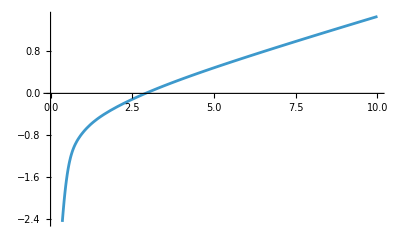

```mathematica
(* Hamiltonium *)
T=(√(mi^2+p^2)+√(mj^2+p^2))*OCen;
βij=(1+p^2/((p^2+mi^2)^(1/2)(p^2+mj^2)^(1/2)))*OCen;
δij=(mi*mj)/((p^2+mi^2)^(1/2)(p^2+mj^2)^(1/2))*OCen;
δii=(mi*mi)/((p^2+mi^2)^(1/2)(p^2+mi^2)^(1/2))*OCen;
δjj=(mj*mj)/((p^2+mj^2)^(1/2)(p^2+mj^2)^(1/2))*OCen;
σij=√(σ0^2(1/2+1/2((4mi*mj)/(mi+mj)^2)^4)+s^2((2mi*mj)/(mi+mj))^2);
σkij=Table[(γk[[k]]*σij)/(√(γk[[k]]^2+σij^2)),{k,1,3}];
VCoul=Cij*Sum[αk[[k]]/r Erf[σkij[[k]]*r],{k,1,3}]*OCen;
Vconf=(-3/4 Cij*c-3/4 Cij*b*r(Exp[-σij^2 r^2]/(√π σij*r)+(1+1/(2 σij^2 r^2))Erf[σij*r]))*OCen;
Vcont=(32OSdS)/(9mi*mj √π)Sum[αk[[k]] σkij[[k]]^3 Exp[-σkij[[k]]^2 r^2],{k,1,3}];
Vtens=OTen/(3mi*mj)*(1/r D[VCoul,{r,1}]-D[VCoul,{r,2}]);
Vsoνi=1/r D[VCoul,{r,1}](OS1L/(2 mi^2));
Vsoνj=1/r D[VCoul,{r,1}](-OS2L/(2 mj^2));
Vsoνij=1/r D[VCoul,{r,1}](-(OS1L-OS2L)/(2mi*mj));
Vsosi=1/r D[Vconf,{r,1}](-OS1L/(2 mi^2));
Vsosj=1/r D[Vconf,{r,1}](OS2L/(2 mj^2));
V=βij^(1/2+ϵCoul)*VCoul*βij^(1/2+ϵCoul)+Vconf+δij^(1/2+ϵcont)*Vcont*δij^(1/2+ϵcont)+δij^(1/2+ϵtens)*Vtens*δij^(1/2+ϵtens)+δii^(1/2+ϵsoν)*Vsoνi*δii^(1/2+ϵsoν)+δjj^(1/2+ϵsoν)*Vsoνj*δjj^(1/2+ϵsoν)+δij^(1/2+ϵsoν)*Vsoνij*δij^(1/2+ϵsoν)+δii^(1/2+ϵsos)*Vsosi*δii^(1/2+ϵsos)+δjj^(1/2+ϵsos)*Vsosj*δjj^(1/2+ϵsos)/.{p->0}
Plot[V,{r,0,10}]
```

```mathematica
(* Matrix elements *)
NSL={};
Do[NSL=Join[NSL,{{n,SL[[i,4]],i}}],{i,1,Length[SL]},{n,1,nmax}];
NSL
mT=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*T[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mβijCoul=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(βij^(1/2+ϵCoul))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mδijcont=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δij^(1/2+ϵcont))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVCoul=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*VCoul[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVconf=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vconf[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVcont=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vcont[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];

If[OTen[[0,0]]!=0 || OTen[[0,0]]==0 && Length[OTen]!=1,
mδijtens=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δij^(1/2+ϵtens))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVtens=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vtens[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

If[OS1L[[0,0]]!=0 || OS1L[[0,0]]==0 && Length[OS1L]!=1,
mδiisoν=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δii^(1/2+ϵsoν))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsoνi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsoνi[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mδiisos=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δii^(1/2+ϵsos))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsosi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsosi[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

If[OS2L[[0,0]]!=0 || OS2L[[0,0]]==0 && Length[OS2L]!=1,
mδjjsoν=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δjj^(1/2+ϵsoν))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsoνj=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsoνj[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mδjjsos=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δjj^(1/2+ϵsos))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsosj=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsosj[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

If[OS1L[[0,0]]!=0 || OS2L[[0,0]]!=0 || (OS1L[[0,0]]==0 && OS2L[[0,0]]==0 && Length[OS1L]!=1 && Length[OS2L]!=1),
mδijsoν=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δij^(1/2+ϵsoν))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsoνij=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsoνij[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

Nfi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
```

{{1,0,1},{2,0,1},{3,0,1},{4,0,1},{5,0,1},{6,0,1},{7,0,1},{8,0,1},{9,0,1},{10,0,1},{11,0,1},{12,0,1},{13,0,1},{14,0,1},{15,0,1},{16,0,1},{17,0,1},{18,0,1},{19,0,1},{20,0,1}}

```mathematica
(* Eigen system *)
RX=RandomReal[{-1,1},{Length[Nfi],Length[Nfi]}];
RX=RX+Transpose[RX];
vt=Eigenvectors[{RX,Nfi}];
vt=vt/Sqrt[Diagonal[vt.Nfi.Transpose[vt]]];
getNm[vt_,M_]:=vt.M.Transpose[vt]

mTt=getNm[vt,mT];
mβijCoult=getNm[vt,mβijCoul];
mδijcontt=getNm[vt,mδijcont];
mVCoult=getNm[vt,mVCoul];
mVconft=getNm[vt,mVconf];
mVcontt=getNm[vt,mVcont];
Hfi=mTt+mβijCoult.mVCoult.mβijCoult+mVconft+mδijcontt.mVcontt.mδijcontt;

If[OTen[[0,0]]!=0 || OTen[[0,0]]==0 && Length[OTen]!=1,
mδijtenst=getNm[vt,mδijtens];
mVtenst=getNm[vt,mVtens];
Hfi=Hfi+mδijtenst.mVtenst.mδijtenst;
];

If[OS1L[[0,0]]!=0 || OS1L[[0,0]]==0 && Length[OS1L]!=1,
mδiisoνt=getNm[vt,mδiisoν];
mVsoνit=getNm[vt,mVsoνi];
mδiisost=getNm[vt,mδiisos];
mVsosit=getNm[vt,mVsosi];
Hfi=Hfi+mδiisoνt.mVsoνit.mδiisoνt+mδiisost.mVsosit.mδiisost;
];

If[OS2L[[0,0]]!=0 || OS2L[[0,0]]==0 && Length[OS2L]!=1,
mδjjsoνt=getNm[vt,mδjjsoν];
mVsoνjt=getNm[vt,mVsoνj];
mδjjsost=getNm[vt,mδjjsos];
mVsosjt=getNm[vt,mVsosj];
Hfi=Hfi+mδjjsoνt.mVsoνjt.mδjjsoνt+mδjjsost.mVsosjt.mδjjsost;
];

If[OS1L[[0,0]]!=0 || OS2L[[0,0]]!=0 || (OS1L[[0,0]]==0 && OS2L[[0,0]]==0 && Length[OS1L]!=1 && Length[OS2L]!=1),
mδijsoνt=getNm[vt,mδijsoν];
mVsoνijt=getNm[vt,mVsoνij];
Hfi=Hfi+mδijsoνt.mVsoνijt.mδijsoνt;
];

{e1,v1}=Transpose[Sort[Transpose[Eigensystem[Hfi]],#1[[1]]<#2[[1]]&]];
e1
v=v1.vt
```

{2.96711,3.62586,4.0636,4.42012,4.73235,5.01371,5.29491,5.56509,5.86424,6.36511,6.5747,7.44826,7.70561,8.67742,9.69427,10.2698,12.3651,12.6003,15.2273,19.4125}

{{0.125837,-0.208609,0.476029,-0.408497,0.766571,-0.356067,0.847436,-0.387265,0.463572,-0.364828,0.282389,-0.209543,0.149385,-0.102161,0.0664648,-0.0403562,0.0220438,-0.0101257,0.00343457,-0.000630506},{-0.0997913,0.160758,-0.39567,0.303663,-0.735084,0.120384,-0.885868,1.1286,0.490413,0.263676,-0.193379,0.144709,-0.102996,0.069959,-0.0451277,0.0271683,-0.0147269,0.00672099,-0.00226779,0.000414627},{-0.0963851,0.156701,-0.409616,0.312572,-0.907266,0.06319,-0.993961,4.65811,-1.95099,-1.60888,0.345612,-0.147865,0.0728253,-0.0382903,0.0206127,-0.0109239,0.00541917,-0.00232851,0.000754833,-0.000134452},{0.0905358,-0.121875,0.321132,-0.0530265,0.559247,1.15132,-1.9037,-7.78787,16.0174,-9.47032,1.65384,-0.954738,0.584147,-0.360179,0.21752,-0.125036,0.0655923,-0.0292501,0.00971104,-0.00175574},{0.0469329,0.135436,-0.470197,1.90612,-3.28665,9.48455,-21.3843,19.3795,4.58377,-24.7728,22.0054,-11.369,6.59849,-3.92568,2.31123,-1.30444,0.675373,-0.298391,0.0984264,-0.0177163},{0.0341404,0.23123,-0.785136,2.86422,-5.36916,15.8876,-46.9085,84.191,-93.3341,63.6026,-23.3968,3.34282,-0.412423,-0.168863,0.229403,-0.172201,0.102665,-0.0490646,0.0169424,-0.00313353},{0.277587,-1.15906,3.64118,-7.70895,17.0551,-26.7516,14.2659,32.173,-92.5598,130.175,-122.316,82.5099,-45.7642,25.9311,-14.6932,8.06085,-4.08865,1.7801,-0.581116,0.103844},{0.650106,-3.15917,10.3104,-24.3844,57.3164,-117.106,180.859,-213.241,198.494,-144.871,76.1734,-22.2412,-0.769001,3.83368,-3.17864,2.05641,-1.13687,0.519568,-0.174459,0.0316951},{0.0972013,-0.251263,1.11672,-2.97233,13.5483,-45.5712,99.0804,-160.677,215.428,-249.697,248.419,-203.593,133.27,-74.2164,40.6597,-21.6693,10.7532,-4.60818,1.4876,-0.263767},{1.08978,-7.51949,24.6499,-65.9882,130.576,-185.509,201.671,-179.123,133.246,-77.452,21.1171,24.5446,-46.2264,41.597,-26.5301,15.0667,-7.70357,3.35011,-1.08926,0.193786},{0.450744,-3.33512,11.4784,-33.6269,74.6468,-123.12,164.572,-195.737,221.233,-244.018,258.744,-250.474,205.848,-135.989,75.0481,-39.2309,19.0739,-8.03937,2.56321,-0.450438},{0.80066,-4.05818,13.0277,-24.2431,26.3335,-13.4445,-10.9966,41.8373,-77.0145,116.731,-159.89,198.898,-215.819,191.31,-131.219,71.6452,-34.9274,14.618,-4.62212,0.806437},{3.40132,-18.1203,62.2221,-133.554,195.279,-219.648,211.134,-187.823,163.178,-142.666,126.359,-111.066,91.9138,-66.13,38.4376,-18.3351,8.14903,-3.20985,0.976186,-0.166173},{-0.0067219,-0.0245521,-1.86674,8.37017,-19.2375,32.3179,-46.5078,62.4306,-81.6989,106.191,-137.197,173.356,-206.428,217.816,-187.838,123.047,-61.1902,25.2726,-7.85352,1.35016},{-5.26888,37.969,-99.9438,154.981,-175.391,165.037,-140.512,114.007,-90.6767,71.5115,-55.7918,42.2656,-29.684,17.4083,-6.37324,-0.804223,2.64919,-1.56319,0.560057,-0.103015},{0.353787,-3.18777,9.91009,-18.6843,27.0811,-34.6038,42.2507,-51.4137,63.4707,-79.8185,101.851,-130.368,163.578,-192.993,200.309,-167.07,101.711,-43.0839,13.2382,-2.23911},{2.34059,-7.54757,11.361,-10.3849,5.07126,2.67013,-11.632,21.6314,-33.1615,47.1138,-64.6359,86.9173,-114.468,145.108,-170.187,172.325,-135.94,73.0873,-23.1531,3.87465},{-18.9298,65.9745,-114.041,136.735,-133.525,116.833,-97.0858,79.3526,-65.1945,54.6455,-47.2607,42.5081,-39.7941,38.2286,-36.2095,31.365,-22.1785,11.0561,-3.31954,0.536695},{-0.355252,1.58375,-3.75229,6.56159,-9.79014,13.4623,-17.794,23.1245,-29.8987,38.6842,-50.1935,65.252,-84.5626,107.917,-132.27,148.622,-141.444,100.535,-43.523,7.52854},{-0.170293,0.811657,-2.06246,3.85075,-6.07233,8.71566,-11.8803,15.7579,-20.6203,26.8214,-34.8046,45.0883,-58.1676,74.1932,-92.1596,108.306,-114.286,98.8848,-59.84,18.0642}}

0.881269 ⅇ^(-3.89386 r^2)-1.01563 ⅇ^(-2.39802 r^2)+1.61118 ⅇ^(-1.47682 r^2)-0.961179 ⅇ^(-0.909497 r^2)+1.25393 ⅇ^(-0.560112 r^2)-0.40491 ⅇ^(-0.344944 r^2)+0.669944 ⅇ^(-0.212433 r^2)-0.212836 ⅇ^(-0.130827 r^2)+0.177116 ⅇ^(-0.0805693 r^2)-0.0969026 ⅇ^(-0.0496184 r^2)+0.0521436 ⅇ^(-0.0305574 r^2)-0.0268987 ⅇ^(-0.0188187 r^2)+0.0133312 ⅇ^(-0.0115895 r^2)-0.00633799 ⅇ^(-0.00713736 r^2)+0.00286659 ⅇ^(-0.00439553 r^2)-0.00121001 ⅇ^(-0.00270698 r^2)+0.000459485 ⅇ^(-0.00166709 r^2)-0.000146729 ⅇ^(-0.00102667 r^2)+0.0000345993 ⅇ^(-0.000632275 r^2)-4.41559×10^-6 ⅇ^(-0.000389386 r^2)

1.93622

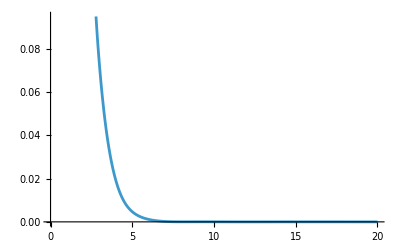

0.287736

```mathematica
(* RMS *)
n=1;
ϕr=Sum[v[[n,i]]*Rnlr[r,i,L],{i,1,Length[v]}]//Simplify
ϕr/.r->0 
Plot[ϕr,{r,0,20}]
rms=Sqrt[NIntegrate[ϕr^2*r^4,{r,0,Infinity}]];
rms/fm
```

```mathematica
(* SHO *)
Rnlp[p_,n_,l_,β_]:=((-1)^n*(-ⅈ)^l)/β^(3/2)*√((2*n!)/Gamma[n+l+3/2])*(p/β)^l ⅇ^(-p^2/(2*β^2))*LaguerreL[n,l+1/2,p^2/β^2]
Rnlr[r_,n_,l_,β_]:=β^(3/2)*√((2*n!)/Gamma[n+l+3/2])*(r*β)^l Exp[-(r^2*β^2)/2]*LaguerreL[n,l+1/2,r^2*β^2]
Solve[NIntegrate[ϕr^2*r^4,{r,0,Infinity}]==Integrate[Rnlr[r,n-1,L,β]^2*r^4,{r,0,Infinity}]&&β>0,β]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→0.839926}}